## part 1 - simulation

#### Defining a Channel

i.i.d Complex Gaussian Channel ,Correlative Channel,Correlative Channel

```mathematica
(*Set the parameters*)
k=30; (*Number of users*)
P=5;  (*Transmission power in Watts*)
t=2; (*Number of antena in BS*)
repeat =5000;
Puniformal = P/t// N;
users = Table[i,{i,k}];
UsersS=15;
CH1 :=Table[RandomVariate[NormalDistribution[0,0.5]] +I*RandomVariate[NormalDistribution[0,0.5]],{t},{k}]
Print["Channel 1-i.i.d Complex Gaussian Channel"]
CH1//MatrixForm
sigma :=RandomVariate[UniformDistribution[{0,3}]];
mu := RandomVariate[UniformDistribution[{0,1}]];
CH2 := Table[RandomVariate[NormalDistribution[mu,sigma]] +I*RandomVariate[NormalDistribution[mu,sigma]],{t},{k}]
Print["Channel 2-Chaotic Channel"]
CH2 //MatrixForm
CH3:=ConstantArray[Table[RandomVariate[NormalDistribution[0,1]] +I*RandomVariate[NormalDistribution[0,1]],{k}],{t}];
Print["Channel 3-Correlative Channel"]
CH3 //MatrixForm
```

Channel 1-i.i.d Complex Gaussian Channel

(0.379497+0.214587 ⅈ | 0.997365+0.850567 ⅈ | -0.243107-0.443866 ⅈ | -0.824912-0.0402584 ⅈ | -0.155529-0.256639 ⅈ | 0.0843666-0.0668391 ⅈ | 0.470649-0.220486 ⅈ | -0.614748-0.846109 ⅈ | -1.03835+0.648179 ⅈ | -0.416337+0.282176 ⅈ | -0.216127+0.261386 ⅈ | -0.48767+0.65099 ⅈ | -0.883533+0.0563868 ⅈ | -0.428826-0.0442866 ⅈ | 0.0987143-0.0802171 ⅈ | 0.848863+1.1145 ⅈ | 0.126143+0.0851136 ⅈ | -0.0407155-0.266825 ⅈ | 0.197264+0.381196 ⅈ | -0.440202+0.541038 ⅈ | -0.130307+0.64725 ⅈ | -0.348615-0.204921 ⅈ | 0.22611+0.51685 ⅈ | -0.544342-0.361665 ⅈ | -0.218371-1.2427 ⅈ | 0.541499-0.295475 ⅈ | -1.22737+0.119255 ⅈ | -0.172955-0.850941 ⅈ | -0.352858+0.37156 ⅈ | 1.17479+0.0425584 ⅈ
-0.287775+0.418698 ⅈ | 0.203507+0.154641 ⅈ | 0.297305+0.25972 ⅈ | -0.507506+0.0329278 ⅈ | -0.21862+0.195553 ⅈ | -0.0437116-0.338341 ⅈ | -0.34143-1.17703 ⅈ | 0.0509412-0.00983613 ⅈ | -0.228179-1.20763 ⅈ | -0.464046-0.347213 ⅈ | 0.399769+0.311612 ⅈ | 0.307073+1.08374 ⅈ | -0.495561+0.479961 ⅈ | -0.21723+0.907623 ⅈ | 0.529997+0.734048 ⅈ | -0.560557+0.120007 ⅈ | -0.167811+0.603472 ⅈ | 0.0593893+0.646455 ⅈ | -0.109953-0.201248 ⅈ | -0.247927+0.687753 ⅈ | -0.608323+0.287412 ⅈ | -0.492044+0.24491 ⅈ | 0.125333-0.233915 ⅈ | -0.222962-0.0370378 ⅈ | -0.118503-0.40782 ⅈ | -0.317229+0.876098 ⅈ | -0.217111-0.162011 ⅈ | -0.141862-0.829682 ⅈ | 0.168077-0.550751 ⅈ | 0.111335+0.402239 ⅈ)

Channel 2-Chaotic Channel

(0.975373+0.62975 ⅈ | -1.5762+1.15975 ⅈ | 0.369228-2.47803 ⅈ | 0.118085+0.828089 ⅈ | -0.00792273-1.67635 ⅈ | 4.46919-0.568743 ⅈ | 0.868909+1.01829 ⅈ | -0.64954+1.95728 ⅈ | 1.66093-2.18553 ⅈ | 0.955926+0.81276 ⅈ | -0.965254+3.35259 ⅈ | 1.46527-0.869724 ⅈ | 0.95894+1.04119 ⅈ | 0.0243901+0.296331 ⅈ | 3.21157+0.39765 ⅈ | -0.820771+0.215537 ⅈ | 0.590771+0.650778 ⅈ | -2.59022+1.67412 ⅈ | -0.0185352+0.866689 ⅈ | -0.331348+0.885417 ⅈ | 0.472261+0.0850783 ⅈ | 1.37301+1.4764 ⅈ | 2.09303+1.52673 ⅈ | -0.309642+0.120549 ⅈ | -0.375131+1.82551 ⅈ | 1.32665+1.82442 ⅈ | 0.270907+0.373443 ⅈ | 1.40492+0.822193 ⅈ | -1.29214+0.225308 ⅈ | -0.469053+0.17446 ⅈ
-0.618404-2.14964 ⅈ | 1.17792+1.91493 ⅈ | 0.274565+0.330296 ⅈ | -0.477546+1.16552 ⅈ | -1.48515-3.06047 ⅈ | -4.26537+0.759742 ⅈ | 0.346336+1.04266 ⅈ | 0.725146+1.40985 ⅈ | 0.292994+1.41766 ⅈ | 0.771436+0.418261 ⅈ | 0.940838+0.398991 ⅈ | 1.87232-0.143968 ⅈ | -0.416248+0.0575077 ⅈ | 0.187139+0.753228 ⅈ | 0.922379+0.905496 ⅈ | 3.5668+2.09432 ⅈ | 0.635488+0.780912 ⅈ | -2.60642+1.39667 ⅈ | -0.714012+1.43801 ⅈ | -3.22644+1.68522 ⅈ | 0.230824+0.240766 ⅈ | -1.30102+1.73519 ⅈ | 1.3318+0.560991 ⅈ | -3.05071-2.11821 ⅈ | -0.213336+1.29042 ⅈ | 0.663963+1.28696 ⅈ | 1.96581-1.49876 ⅈ | 0.218635+2.40131 ⅈ | -5.0727+1.45025 ⅈ | 0.733891+0.510058 ⅈ)

Channel 3-Correlative Channel

(-0.424636-0.545677 ⅈ | 0.117776-1.52428 ⅈ | -0.667918+0.989989 ⅈ | 1.2032-0.524137 ⅈ | 0.218194+0.0159911 ⅈ | -1.47904+2.45677 ⅈ | 0.451123+0.874206 ⅈ | -0.677949+0.620804 ⅈ | -0.602904-1.3201 ⅈ | -0.743199-0.931348 ⅈ | 0.588061-0.739136 ⅈ | 0.911519-1.52938 ⅈ | 1.47612+0.171027 ⅈ | -2.7882-0.0288342 ⅈ | -0.257519-0.950822 ⅈ | -0.836774-0.984768 ⅈ | 0.847657-0.0230534 ⅈ | 1.11922-0.0394586 ⅈ | 0.418666-0.5595 ⅈ | 0.531985+0.624312 ⅈ | 0.538606+0.889637 ⅈ | 0.207735-1.57504 ⅈ | -0.339375+0.589012 ⅈ | -0.224988-1.52248 ⅈ | -0.953527-0.561376 ⅈ | 0.104044+0.861612 ⅈ | -0.177014-1.04693 ⅈ | 0.469064-2.03706 ⅈ | -1.72808+0.000594211 ⅈ | 1.70076-2.16185 ⅈ
-0.424636-0.545677 ⅈ | 0.117776-1.52428 ⅈ | -0.667918+0.989989 ⅈ | 1.2032-0.524137 ⅈ | 0.218194+0.0159911 ⅈ | -1.47904+2.45677 ⅈ | 0.451123+0.874206 ⅈ | -0.677949+0.620804 ⅈ | -0.602904-1.3201 ⅈ | -0.743199-0.931348 ⅈ | 0.588061-0.739136 ⅈ | 0.911519-1.52938 ⅈ | 1.47612+0.171027 ⅈ | -2.7882-0.0288342 ⅈ | -0.257519-0.950822 ⅈ | -0.836774-0.984768 ⅈ | 0.847657-0.0230534 ⅈ | 1.11922-0.0394586 ⅈ | 0.418666-0.5595 ⅈ | 0.531985+0.624312 ⅈ | 0.538606+0.889637 ⅈ | 0.207735-1.57504 ⅈ | -0.339375+0.589012 ⅈ | -0.224988-1.52248 ⅈ | -0.953527-0.561376 ⅈ | 0.104044+0.861612 ⅈ | -0.177014-1.04693 ⅈ | 0.469064-2.03706 ⅈ | -1.72808+0.000594211 ⅈ | 1.70076-2.16185 ⅈ)

## Function

```mathematica
(*to qustion 3*)
rateFunc[P_,Ch_,Vect_, t_]:=Sum[Log2[1+P*Norm[Ch*Vect[[All,i]]]^2],{i,t}]
(*to qustion 4*)
rateStrongFunc[P_,Ch_, t_]:=Sum[Log2[1+P*Ch[[i]]^2],{i,t}]
(*to qustion 4, find all the user whit the strong channel *)
StrongestNorm[t_,Ch_]:=Sort[Table[Norm[Ch[[All,i]]]^2,{i,k}],#1>#2&][[1;;t]]
(*vector - Pseudo Inverse*)
Vec[ch_] :=PseudoInverse[ch];
Totalrate[Ch_,Users_]:=Total[1+Puniformal*Norm/@Ch[[Users]]^2]/UsersS;
(*to qustion 5*)
SubgroupCh[t_,Length_,Ch_,Groups_]:= Table[Table[Ch[[All,Groups[[j,i]]]],{i,t}],{j,Length}];
Totaleate[Ch_,Users_]:=Total[1+Puniformal*Norm/@Ch[[Users]]^2]/(UsersS-1);
SubgroupCalculte[t_,Length_,Ch_,Groups_]:=ParallelMap[Function[j,ParallelMap[Function[i,Ch[[All,Groups[[j,i]]]]],Range[t]]],Range[Length]];
SubgroupCalculte1[t_,Length_,Ch_,Groups_]:=ParallelTable[Ch[[All,Groups[[j,i]]]],{j,Length},{i,t}];
(*to qustion 6 - SUS rate*)
SUSFunc[P_,Ch_,Groups_,t_]:=Table[Log2[1+P*Norm[Ch[[Groups[[i]]]]]^2],{i,t}]
TotalRate[Ch_,Users_]:=Total[1+Puniformal*Norm/@Ch[[Users]]^2];
MaxNormUser[Matrix_]:=Position[Norm/@Matrix,Max[Norm/@Matrix]][[1,1]];
Projections[M1_,M2_]:=M1.ConjugateTranspose[M2];
```

### simulation

1. The BS chooses a single user randomly and transmits to it at maximum power.

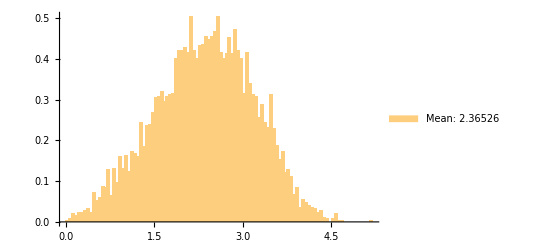
-Graphics-i.i.d Complex Gaussian Channel

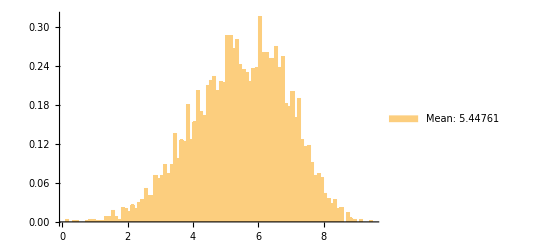
-Graphics-Chaotic Channel

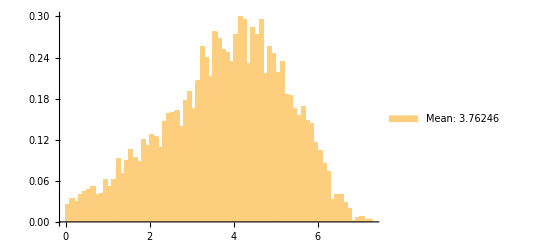
-Graphics-Correlative Channel

```mathematica
singleUser=RandomChoice[users];
CH1Rand:=CH1[[All,singleUser]];
CH2Rand:=CH2[[All,singleUser]];
CH3Rand:=CH3[[All,singleUser]];
rate2CH1:=Log2[1+P*Norm[CH1Rand]^2];
rate2CH2:=Log2[1+P*Norm[CH2Rand]^2];
rate2CH3:=Log2[1+P*Norm[CH3Rand]^2];
Labeled[Histogram[ParallelTable[rate2CH1,{repeat}],80,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rate2CH1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[rate2CH2,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rate2CH2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[rate2CH3,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rate2CH3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

2. 	The BS chooses to transmit to a single user with the strongest channel (the user with the highest row norm) and transmits to it at maximum power.

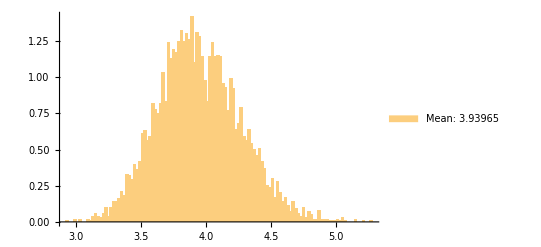
-Graphics-i.i.d Complex Gaussian Channel

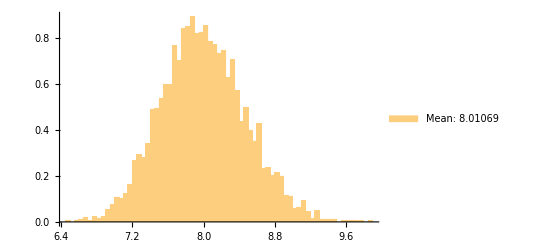
-Graphics-Chaotic Channel

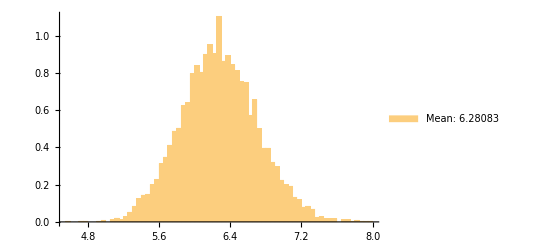
-Graphics-Correlative Channel

```mathematica
rateStrongCH1:=Log2[1+P*Max[Table[Norm[CH1[[All,i]]]^2,{i,k}]]];
rateStrongCH2:=Log2[1+P*Max[Table[Norm[CH2[[All,i]]]^2,{i,k}]]];
rateStrongCH3:=Log2[1+P*Max[Table[Norm[CH3[[All,i]]]^2,{i,k}]]];
Labeled[Histogram[ParallelTable[rateStrongCH1,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rateStrongCH1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[rateStrongCH2,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rateStrongCH2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[rateStrongCH3,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rateStrongCH3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

3. 	The BS chooses to transmit to 𝑡 randomly chosen users using ZFBF with uniform power allocation between the selected users .

```mathematica
Puniformal = P/t// N;
multiUsers = RandomSample[users,t];
CH1Trand:=Table[CH1[[All,multiUsers[[i]]]],{i,t}];
CH2Trand:=Table[CH2[[All,multiUsers[[i]]]],{i,t}];
CH3Trand:=Table[CH3[[All,multiUsers[[i]]]],{i,t}];
ratetRand1:=rateFunc[Puniformal,CH1Trand,Transpose[Map[Normalize,Transpose[PseudoInverse[CH1Trand]]]], t];
ratetRand2:=rateFunc[Puniformal,CH2Trand,Transpose[Map[Normalize,Transpose[PseudoInverse[CH2Trand]]]], t];
ratetRand3:=rateFunc[Puniformal,CH3Trand,Transpose[Map[Normalize,Transpose[PseudoInverse[CH3Trand]]]], t];
```

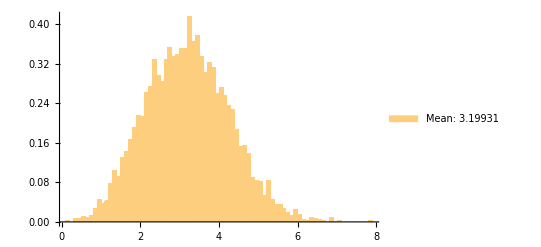
-Graphics-i.i.d Complex Gaussian Channel

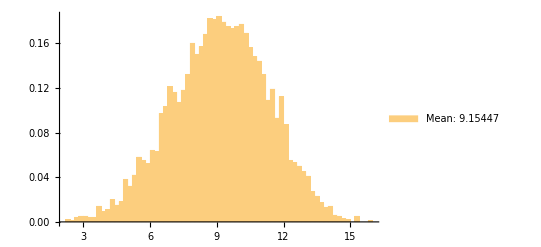
-Graphics-Chaotic Channel

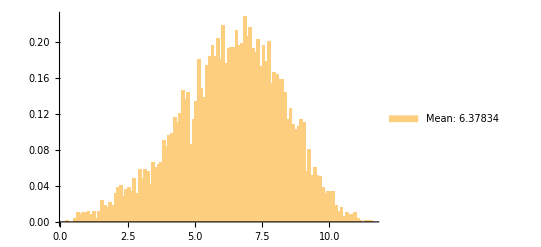
-Graphics-Correlative Channel

```mathematica
(*Output grahp*)
Labeled[Histogram[ParallelTable[ratetRand1,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetRand1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[ratetRand2,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetRand2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[ratetRand3,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetRand3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

4.  The base station chooses to transmit to the t strongest users using ZFBF, so that the power is equally distributed between the selected users .

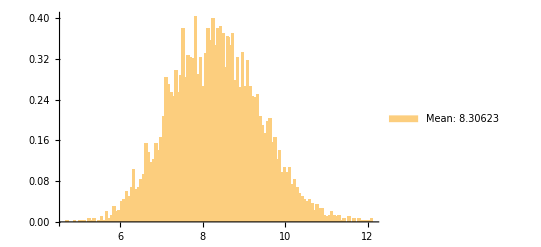
-Graphics-i.i.d Complex Gaussian Channel

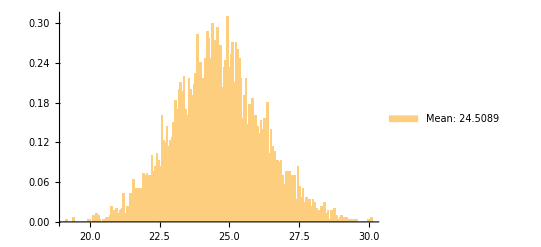
-Graphics-Chaotic Channel

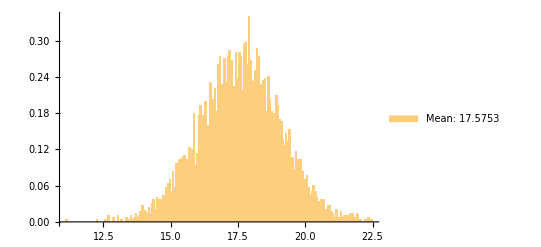
-Graphics-Correlative Channel

```mathematica
ratetStrongestCH1:=rateStrongFunc[Puniformal,StrongestNorm[t,CH1],t];
ratetStrongestCH2:=rateStrongFunc[Puniformal,StrongestNorm[t,CH2],t];
ratetStrongestCH3:=rateStrongFunc[Puniformal,StrongestNorm[t,CH3],t];
Labeled[Histogram[ParallelTable[ratetStrongestCH1,{repeat}],120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetStrongestCH1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[ratetStrongestCH2,{repeat}],120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetStrongestCH2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[ratetStrongestCH3,{repeat}],120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetStrongestCH3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

5. The BS tests all user subgroups of the size 𝑡, and transmits to the optimal group (e.g., with the highest rates) using ZFBF. The power allocation is uniform between the selected users.

```mathematica
SubGroupst =Subsets[users, {t}]
```

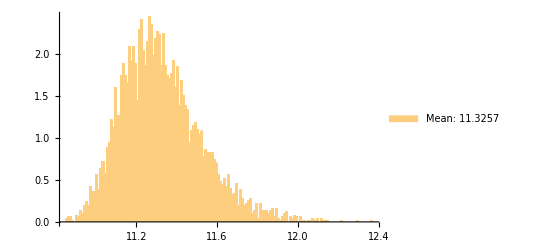
-Graphics-i.i.d Complex Gaussian Channel

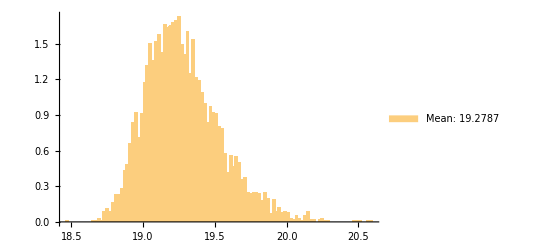
-Graphics-Chaotic Channel

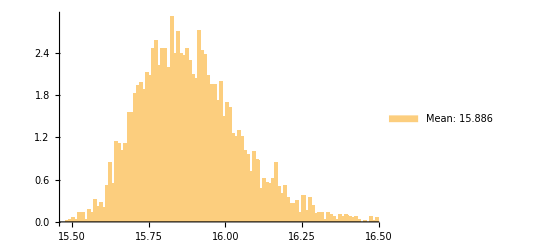
-Graphics-Correlative Channel

```mathematica
t = 2;
SubGroupst =Subsets[users, {t}];
L=Length[SubGroupst];
ListNumGroup = Table[i,{i,L}];
(*Using the function from qustion 3*)
OptimalGroupRateCH1:=Max[Table[rateFunc[Puniformal,CH1,Transpose[Map[Normalize,Transpose[PseudoInverse[SubgroupCh[t,L,CH1,SubGroupst][[j]]]]]] , t],{j,L}]];
res1=ParallelTable[OptimalGroupRateCH1,{repeat}];
Labeled[Histogram[res1,120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[res1]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
OptimalGroupRateCH2:=Max[Table[rateFunc[Puniformal,CH2,Transpose[Map[Normalize,Transpose[PseudoInverse[SubgroupCh[t,L,CH2,SubGroupst][[j]]]]]] , t],{j,L}]];
res2=ParallelTable[OptimalGroupRateCH2,{repeat}];
Labeled[Histogram[res2,120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[res2]]},Bottom]],"Chaotic Channel",Top]
OptimalGroupRateCH3:=Max[Table[rateFunc[Puniformal,CH3,Transpose[Map[Normalize,Transpose[PseudoInverse[SubgroupCh[t,L,CH3,SubGroupst][[j]]]]]]  , t],{j,L}]];
res3=ParallelTable[OptimalGroupRateCH3,{repeat}];
Labeled[Histogram[res3,120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[res3]]},Bottom]],"Correlative Channel",Top]
```

#### Bonus

SUS Algorithm

```mathematica
(*Example complex-valued channel matrix*)
```

```mathematica
t=2;
channel1=Table[
(* channel matrix*)
channelMatrix=Transpose[CH1];
(*Select the channel responses of the selected users, The user whit the max Norm*)
nullSpace=NullSpace[{channelMatrix[[MaxNormUser[channelMatrix]]]}];(*Calculate the null space of the selected channel matrix*)
selectedUsers={MaxNormUser[channelMatrix]};
projections=nullSpace.ConjugateTranspose[channelMatrix];
maxNormUser2:=Position[Norm/@Transpose[projections],Max[Norm/@Transpose[projections]]][[1,1]];
selectedUsers=Append[selectedUsers,maxNormUser2];
nullSpace=Append[nullSpace,NullSpace[{channelMatrix[[maxNormUser2]]}][[1]]];
nullSpace= NullSpace[{nullSpace[[1]]}][[1]];
selectedUsers=DeleteDuplicates[selectedUsers];
If[Length[selectedUsers] == 1,selectedUsers=Append[selectedUsers,MaxNormUser[Transpose[nullSpace]]],Else[Continue]];
selectedUsers=DeleteDuplicates[selectedUsers];
TotalRate[channelMatrix,selectedUsers],{5000}];

channel2=Table[
(* channel matrix*)
channelMatrix=Transpose[CH2];
(*Select the channel responses of the selected users, The user whit the max Norm*)
nullSpace=NullSpace[{channelMatrix[[MaxNormUser[channelMatrix]]]}];(*Calculate the null space of the selected channel matrix*)
selectedUsers={MaxNormUser[channelMatrix]};
projections=nullSpace.ConjugateTranspose[channelMatrix];
maxNormUser2:=Position[Norm/@Transpose[projections],Max[Norm/@Transpose[projections]]][[1,1]];
selectedUsers=Append[selectedUsers,maxNormUser2];
nullSpace=Append[nullSpace,NullSpace[{channelMatrix[[maxNormUser2]]}][[1]]];
nullSpace= NullSpace[{nullSpace[[1]]}][[1]];
selectedUsers=DeleteDuplicates[selectedUsers];
If[Length[selectedUsers] == 1,selectedUsers=Append[selectedUsers,MaxNormUser[Transpose[nullSpace]]],Else[Continue]];
selectedUsers=DeleteDuplicates[selectedUsers];
Totalrate[channelMatrix,selectedUsers],{5000}];

channel3=Table[
(* channel matrix*)
channelMatrix=Transpose[CH3];
(*Select the channel responses of the selected users, The user whit the max Norm*)
nullSpace=NullSpace[{channelMatrix[[MaxNormUser[channelMatrix]]]}];(*Calculate the null space of the selected channel matrix*)
selectedUsers={MaxNormUser[channelMatrix]};
projections=nullSpace.ConjugateTranspose[channelMatrix];
maxNormUser2:=Position[Norm/@Transpose[projections],Max[Norm/@Transpose[projections]]][[1,1]];
selectedUsers=Append[selectedUsers,maxNormUser2];
nullSpace=Append[nullSpace,NullSpace[{channelMatrix[[maxNormUser2]]}][[1]]];
nullSpace= NullSpace[{nullSpace[[1]]}][[1]];
selectedUsers=DeleteDuplicates[selectedUsers];
If[Length[selectedUsers] == 1,selectedUsers=Append[selectedUsers,MaxNormUser[Transpose[nullSpace]]],Else[Continue]];
selectedUsers=DeleteDuplicates[selectedUsers];
Totaleate[channelMatrix,selectedUsers],{5000}];
```

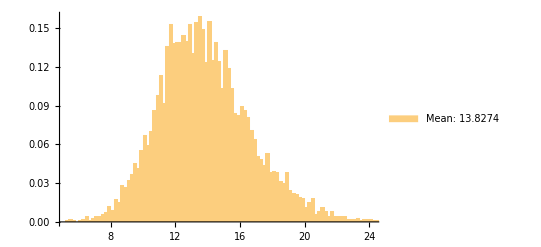
-Graphics-SUS i.i.d Complex Gaussian Channel

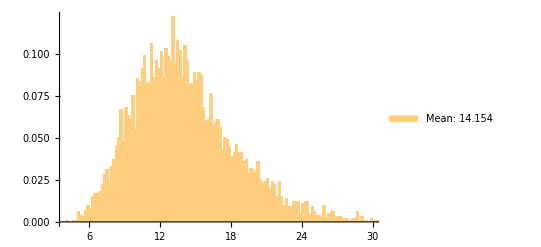
-Graphics-SUS Chaotic Channel

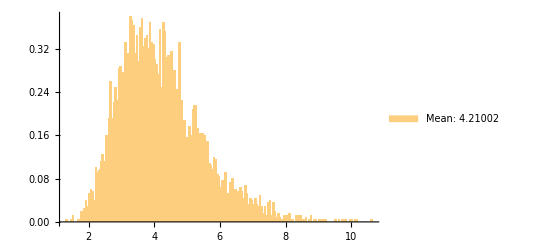
-Graphics-SUS Correlative Channel

```mathematica
Labeled[Histogram[channel1,150,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[channel1]]},Bottom]],"SUS i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[channel2,150,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[channel2]]},Bottom]],"SUS Chaotic Channel",Top]
Labeled[Histogram[channel3,150,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[channel3]]},Bottom]],"SUS Correlative Channel",Top]
```

```mathematica
(*Select the channel responses of the selected users, The user whit the max Norm*)
nullSpace=NullSpace[{channelMatrix[[MaxNormUser[channelMatrix]]]}];(*Calculate the null space of the selected channel matrix*)
selectedUsers={MaxNormUser[channelMatrix]};
projections=nullSpace.ConjugateTranspose[channelMatrix];
maxNormUser2:=Position[Norm/@Transpose[projections],Max[Norm/@Transpose[projections]]][[1,1]]selectedUsers=Append[selectedUsers,maxNormUser2];
nullSpace=Append[nullSpace,NullSpace[{channelMatrix[[maxNormUser2]]}][[1]]];
nullSpace= NullSpace[{nullSpace[[1]]}][[1]];
selectedUsers=DeleteDuplicates[selectedUsers];
```

## part 2 - simulation

```mathematica
(*Transmission power in Watts*)
P=5;  
Mr=4;   
Mt=4;
M = 5000;
Listplot ={};
Puniformal = P/Mt;
(*Symbol range*)
Uniform = Table[i, {i,-4,4}] ;
(*Channel*)
ChannelGaussian=Table[RandomVariate[NormalDistribution[0,1]] ,{Mr},{Mt}];
Print["Channel - Gaussian Channel"]
ChannelGaussian//MatrixForm
```

Channel - Gaussian Channel

(0.398846 | -0.595273 | -0.898689 | 1.0269
0.649936 | 2.10193 | 0.965995 | -1.32402
0.191942 | 0.0832217 | -0.640068 | 0.322801
0.407587 | 1.86457 | -1.65608 | 0.281297)

#### Function

```mathematica
MSE[H_,Hest_,Mr_,Mt_,M_] := ∑_(i=1)^M (NormaL2[(H - Hest[[i]])]/(Mr*Mt*M));
NormaL2[Vect_]:=∑_(j=1)^(Dimensions[Vect][[1]]) √(∑_(i=1)^(Dimensions[Vect][[2]]) (Vect[[j]][[i]])^2)
```

#### Simulation 1

N = Mr = 4

```mathematica
Mr=4;
(*Matrix size 4x4*)
ListSymbol1 = Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol=ListSymbol1/Norm[ListSymbol1] //N;
ListSymbol1//MatrixForm;
NormaListSymbol//MatrixForm;
(*Transmited*)
tembel=√Puniformal*NormaListSymbol;
Y:= ChannelGaussian.tembel+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol=ParallelTable[PseudoInverse[Y].ChannelGaussian,{M}];
S1=MSE[tembel,TableSymbol,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S1]]
```

{11.2415}

#### Simulation 2

N = Mr + 1= 5

```mathematica
Mr=5;
(*Matrix size 4x5*)
ListSymbol2 = Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol2=ListSymbol2/Norm[ListSymbol2] //N ;
ListSymbol2//MatrixForm;
NormaListSymbol2//MatrixForm;
Norm[ListSymbol2]//N;
(*Transmited*)
tembel2=√Puniformal*NormaListSymbol2;
Y2:= ChannelGaussian.tembel2+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol2=ParallelTable[Transpose[PseudoInverse[Y2].ChannelGaussian],{M}];
S2=MSE[tembel2,TableSymbol2,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S2]]
```

{11.2415,-17.7703}

#### Simulation 3

N = Mr + 2 = 6

```mathematica
Mr=6;
(*Matrix size 4x6*)
ListSymbol3 = Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol3=ListSymbol3/Norm[ListSymbol3] //N ;
ListSymbol3//MatrixForm;
NormaListSymbol3//MatrixForm;
Norm[ListSymbol3]//N;
(*Transmited*)
tembel3=√Puniformal*NormaListSymbol3;
Y3:= ChannelGaussian.tembel3+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol3=ParallelTable[Transpose[PseudoInverse[Y3].ChannelGaussian],{M}];
S3=MSE[tembel3,TableSymbol3,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S3]]
```

{11.2415,-17.7703,-35.3325}

#### Simulation 4

N = Mr + 3 = 7

```mathematica
Mr=7;
(*Matrix size 4x7*)
ListSymbol4= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol4=ListSymbol4/Norm[ListSymbol4] //N ;
ListSymbol4//MatrixForm;
NormaListSymbol4//MatrixForm;
Norm[ListSymbol4]//N;
(*Transmited*)
tembel4=√Puniformal*NormaListSymbol4;
Y4:= ChannelGaussian.tembel4+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol4=ParallelTable[Transpose[PseudoInverse[Y4].ChannelGaussian],{M}];
S4=MSE[tembel4,TableSymbol4,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S4]]
```

{11.2415,-17.7703,-35.3325,-48.8979}

#### Simulation 5

N = Mr + 4 = 8

```mathematica
Mr=8;
(*Matrix size 4x8*)
ListSymbol5= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol5=ListSymbol5/Norm[ListSymbol5] //N ;
(*Transmited*)
tembel5=√Puniformal*NormaListSymbol5;
Y5:= ChannelGaussian.tembel5+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol5=ParallelTable[Transpose[PseudoInverse[Y5].ChannelGaussian],{M}];
S5=MSE[tembel5,TableSymbol5,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S5]]
```

{11.2415,-17.7703,-35.3325,-48.8979,-58.2098}

#### Simulation 6

N = Mr + 4 = 9

```mathematica
Mr=9;
(*Matrix size 4x9*)
ListSymbol6= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol6=ListSymbol6/Norm[ListSymbol6] //N ;
(*Transmited*)
tembel6=√Puniformal*NormaListSymbol6;
Y6:= ChannelGaussian.tembel6+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol6=ParallelTable[Transpose[PseudoInverse[Y6].ChannelGaussian],{M}];
S6=MSE[tembel6,TableSymbol6,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S6]]
```

{11.2415,-17.7703,-35.3325,-48.8979,-58.2098,-64.94}

#### Simulation 6-20

```mathematica
Mr=10;
(*Matrix size 4x10*)
ListSymbol7= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol7=ListSymbol7/Norm[ListSymbol7] //N ;
(*Transmited*)
tembel7=√Puniformal*NormaListSymbol7;
Y7:= ChannelGaussian.tembel7+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol7=ParallelTable[Transpose[PseudoInverse[Y7].ChannelGaussian],{M}];
S7=MSE[tembel7,TableSymbol7,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S7]];
Mr=11;
(*Matrix size 4x11*)
ListSymbol8= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol8=ListSymbol8/Norm[ListSymbol8] //N ;
(*Transmited*)
tembel8=√Puniformal*NormaListSymbol8;
Y8:= ChannelGaussian.tembel8+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol8=ParallelTable[Transpose[PseudoInverse[Y8].ChannelGaussian],{M}];
S8=MSE[tembel8,TableSymbol8,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S8]];
Mr=12;
(*Matrix size 4x12*)
ListSymbol9= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol9=ListSymbol9/Norm[ListSymbol9] //N ;
(*Transmited*)
tembel9=√Puniformal*NormaListSymbol9;
Y9:= ChannelGaussian.tembel9+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol9=ParallelTable[Transpose[PseudoInverse[Y9].ChannelGaussian],{M}];
S9=MSE[tembel9,TableSymbol9,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S9]];
Mr=13;
(*Matrix size 4x13*)
ListSymbol10= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol10=ListSymbol10/Norm[ListSymbol10] //N ;
(*Transmited*)
tembel10=√Puniformal*NormaListSymbol10;
Y10:= ChannelGaussian.tembel10+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol10=ParallelTable[Transpose[PseudoInverse[Y10].ChannelGaussian],{M}];
S10=MSE[tembel10,TableSymbol10,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S10]];
Mr=14;
(*Matrix size 4x14*)
ListSymbol11= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol11=ListSymbol11/Norm[ListSymbol11] //N ;
(*Transmited*)
tembel11=√Puniformal*NormaListSymbol11;
Y11:= ChannelGaussian.tembel11+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol11=ParallelTable[Transpose[PseudoInverse[Y11].ChannelGaussian],{M}];
S11=MSE[tembel11,TableSymbol11,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S11]];
Mr=15;
(*Matrix size 4x15*)
ListSymbol12= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol12=ListSymbol12/Norm[ListSymbol12] //N ;
(*Transmited*)
tembel12=√Puniformal*NormaListSymbol12;
Y12:= ChannelGaussian.tembel12+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol12=ParallelTable[Transpose[PseudoInverse[Y12].ChannelGaussian],{M}];
S12=MSE[tembel12,TableSymbol12,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S12]];
Mr=16;
(*Matrix size 4x16*)
ListSymbol13= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol13=ListSymbol13/Norm[ListSymbol13] //N ;
(*Transmited*)
tembel13=√Puniformal*NormaListSymbol13;
Y13:= ChannelGaussian.tembel13+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol13=ParallelTable[Transpose[PseudoInverse[Y13].ChannelGaussian],{M}];
S13=MSE[tembel13,TableSymbol13,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S13]];
Mr=17;
(*Matrix size 4x17*)
ListSymbol14= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol14=ListSymbol14/Norm[ListSymbol14] //N ;
(*Transmited*)
tembel14=√Puniformal*NormaListSymbol14;
Y14:= ChannelGaussian.tembel14+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol14=ParallelTable[Transpose[PseudoInverse[Y14].ChannelGaussian],{M}];
S14=MSE[tembel14,TableSymbol14,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S14]];
Mr=18;
(*Matrix size 4x18*)
ListSymbol15= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol15=ListSymbol15/Norm[ListSymbol15] //N ;
(*Transmited*)
tembel15=√Puniformal*NormaListSymbol15;
Y15:= ChannelGaussian.tembel15+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol15=ParallelTable[Transpose[PseudoInverse[Y15].ChannelGaussian],{M}];
S15=MSE[tembel15,TableSymbol15,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S15]];
Mr=19;
(*Matrix size 4x19*)
ListSymbol16= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol16=ListSymbol16/Norm[ListSymbol16] //N ;
(*Transmited*)
tembel16=√Puniformal*NormaListSymbol16;
Y16:= ChannelGaussian.tembel16+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol16=ParallelTable[Transpose[PseudoInverse[Y16].ChannelGaussian],{M}];
S16=MSE[tembel16,TableSymbol16,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S16]];
Mr=120;
(*Matrix size 4x20*)
ListSymbol17= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol17=ListSymbol17/Norm[ListSymbol17] //N ;
(*Transmited*)
tembel17=√Puniformal*NormaListSymbol17;
Y17:= ChannelGaussian.tembel17+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol17=ParallelTable[Transpose[PseudoInverse[Y17].ChannelGaussian],{M}];
S17=MSE[tembel17,TableSymbol17,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,20*Log2[S17]]
```

{11.2415,-17.7703,-35.3325,-48.8979,-58.2098,-64.94,-67.1564,-74.7275,-76.829,-75.2502,-80.8943,-80.0687,-84.0321,-84.9719,-90.0926,-88.3068,-140.94}

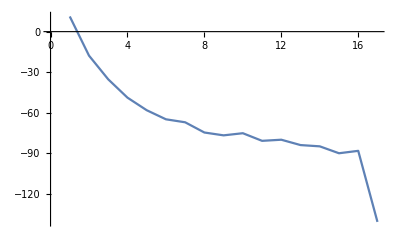

```mathematica
ListLinePlot[Listplot]
```